```mathematica
fY1XG1=1/(1+Exp[-1(α+β*X+γ+ η*X)])
```

1/(1+ⅇ^(-α-X β-γ-X η))

```mathematica
fY1XG0=1/(1+Exp[-1(α+β*X)])
```

1/(1+ⅇ^(-α-X β))

```mathematica
fY0XG1=1-1/(1+Exp[-1(α+β*X+γ+ η*X)])
```

1-1/(1+ⅇ^(-α-X β-γ-X η))

```mathematica
fY0XG0=1-1/(1+Exp[-1(α+β*X)])
```

1-1/(1+ⅇ^(-α-X β))

```mathematica
lY1XG1=Log[fY1XG1]
```

Log[1/(1+ⅇ^(-α-X β-γ-X η))]

```mathematica
lY1XG0=Log[fY1XG0]
```

Log[1/(1+ⅇ^(-α-X β))]

```mathematica
lY0XG1=Log[fY0XG1]
```

Log[1-1/(1+ⅇ^(-α-X β-γ-X η))]

```mathematica
lY0XG0=Log[fY0XG1]
```

Log[1-1/(1+ⅇ^(-α-X β-γ-X η))]

```mathematica
fY1X0G1=fY1XG1
```

1/(1+ⅇ^(-α-X β-γ-X η))

```mathematica
DDfY1X0G1=Simplify[D[D[fY1XG1,X],X]/.X->0]
```

-(ⅇ^(α+γ) (-1+ⅇ^(α+γ)) (β+η)^2)/((1+ⅇ^(α+γ))^3)

```mathematica
fY1X0G0=fY1XG0/.X->0
```

1/(1+ⅇ^-α)

```mathematica
DDfY1X0G0=Simplify[D[D[fY1XG0,X],X]/.X->0]
```

-(ⅇ^α (-1+ⅇ^α) β^2)/((1+ⅇ^α)^3)

```mathematica
fY0X0G1=Simplify[fY0XG1/.X->0]
```

1/(1+ⅇ^(α+γ))

```mathematica
DDfY0X0G1=Simplify[D[D[fY0XG1,X],X]/.X->0]
```

(ⅇ^(α+γ) (-1+ⅇ^(α+γ)) (β+η)^2)/((1+ⅇ^(α+γ))^3)

```mathematica
fY0X0G0=Simplify[fY0XG0/.X->0]
```

1/(1+ⅇ^α)

```mathematica
DDfY0X0G0=Simplify[D[D[fY0XG0,X],X]/.X->0]
```

(ⅇ^α (-1+ⅇ^α) β^2)/((1+ⅇ^α)^3)

```mathematica
EY1G1= (fY1XG1 +.5* D[D[fY1XG1,X],X])/.X->0
```

1/(1+ⅇ^(-α-γ))+0.5 ((2 ⅇ^(-2 α-2 γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^3)-(ⅇ^(-α-γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^2))

```mathematica
EY1G0= (fY1XG0 + .5*D[D[fY1XG0,X],X])/.X->0
```

1/(1+ⅇ^-α)+0.5 ((2 ⅇ^(-2 α) β^2)/((1+ⅇ^-α)^3)-(ⅇ^-α β^2)/((1+ⅇ^-α)^2))

```mathematica
EY0G1=(fY0XG1 + .5*D[D[fY0XG1,X],X])/.X->0
```

1-1/(1+ⅇ^(-α-γ))+0.5 (-(2 ⅇ^(-2 α-2 γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^3)+(ⅇ^(-α-γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^2))

```mathematica
EY0G0=(fY0XG1 + .5*D[D[fY0XG0,X],X])/.X->0
```

1-1/(1+ⅇ^(-α-γ))+0.5 (-(2 ⅇ^(-2 α) β^2)/((1+ⅇ^-α)^3)+(ⅇ^-α β^2)/((1+ⅇ^-α)^2))

```mathematica
R1X=fY1XG1/EY1G1
```

1/((1+ⅇ^(-α-X β-γ-X η)) (1/(1+ⅇ^(-α-γ))+0.5 ((2 ⅇ^(-2 α-2 γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^3)-(ⅇ^(-α-γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^2))))

```mathematica
R2X=fY1XG0/EY1G0
```

1/((1+ⅇ^(-α-X β)) (1/(1+ⅇ^-α)+0.5 ((2 ⅇ^(-2 α) β^2)/((1+ⅇ^-α)^3)-(ⅇ^-α β^2)/((1+ⅇ^-α)^2))))

```mathematica
R3X=fY0XG1/EY0G1
```

(1-1/(1+ⅇ^(-α-X β-γ-X η)))/(1-1/(1+ⅇ^(-α-γ))+0.5 (-(2 ⅇ^(-2 α-2 γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^3)+(ⅇ^(-α-γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^2)))

```mathematica
R4X=fY0XG0/EY0G0
```

(1-1/(1+ⅇ^(-α-X β)))/(1-1/(1+ⅇ^(-α-γ))+0.5 (-(2 ⅇ^(-2 α) β^2)/((1+ⅇ^-α)^3)+(ⅇ^-α β^2)/((1+ⅇ^-α)^2)))

```mathematica
r1x=Log[R1X]
```

Log[1/((1+ⅇ^(-α-X β-γ-X η)) (1/(1+ⅇ^(-α-γ))+0.5 ((2 ⅇ^(-2 α-2 γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^3)-(ⅇ^(-α-γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^2))))]

```mathematica
Simplify[r1x/.γ->0/.η->0]
```

Log[(ⅇ^(X β) (1.+ⅇ^α)^3)/((1.+ⅇ^(α+X β)) (1.+ⅇ^(2 α)+0.5 β^2+ⅇ^α (2.-0.5 β^2)))]

```mathematica
r2x=Log[R2X]
```

Log[1/((1+ⅇ^(-α-X β)) (1/(1+ⅇ^-α)+0.5 ((2 ⅇ^(-2 α) β^2)/((1+ⅇ^-α)^3)-(ⅇ^-α β^2)/((1+ⅇ^-α)^2))))]

```mathematica
r3x=Log[R3X]
```

Log[(1-1/(1+ⅇ^(-α-X β-γ-X η)))/(1-1/(1+ⅇ^(-α-γ))+0.5 (-(2 ⅇ^(-2 α-2 γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^3)+(ⅇ^(-α-γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^2)))]

```mathematica
r4x=Log[R4X]
```

Log[(1-1/(1+ⅇ^(-α-X β)))/(1-1/(1+ⅇ^(-α-γ))+0.5 (-(2 ⅇ^(-2 α) β^2)/((1+ⅇ^-α)^3)+(ⅇ^-α β^2)/((1+ⅇ^-α)^2)))]

```mathematica
EY1G1/.α->-3/.β->.1/.γ->1/.η->0/.ω->.001
```

0.119603

```mathematica
EY1G0/.α->-3/.β->.1/.γ->1/.η->0/.ω->.001
```

0.0476303

```mathematica
Dr1xGamma=Simplify[D[r1x,γ]]
```

-((0.5 ⅇ^(α+γ) (-2.-12. ⅇ^(2 (α+γ))-2. ⅇ^(4 (α+γ))-4. β^2-8. β η-4. η^2+ⅇ^(α+γ) (-8.-6. β^2-12. β η-6. η^2)+ⅇ^(2 α+2 γ+X (β+η)) (12.-6. β^2-12. β η-6. η^2)+ⅇ^(α+γ+X (β+η)) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(3 α+3 γ+X (β+η)) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(X (β+η)) (2.+1. β^2+2. β η+1. η^2)+ⅇ^(4 α+4 γ+X (β+η)) (2.+1. β^2+2. β η+1. η^2)+ⅇ^(3 (α+γ)) (-8.+2. β^2+4. β η+2. η^2)))/((1.+ⅇ^(α+γ))^3 (1.+ⅇ^(α+γ+X (β+η))) (1.+ⅇ^(2 (α+γ))+0.5 β^2+1. β η+0.5 η^2+ⅇ^(α+γ) (2.-0.5 β^2-1. β η-0.5 η^2))))

```mathematica
Dr1xEta=Simplify[D[r1x,η]]
```

((-1.+1. ⅇ^(α+γ)-1. ⅇ^(α+γ+X (β+η))+1. ⅇ^(2 α+2 γ+X (β+η))) (β+η)+X (1.+1. ⅇ^(2 (α+γ))+0.5 β^2+1. β η+0.5 η^2+ⅇ^(α+γ) (2.-0.5 β^2-1. β η-0.5 η^2)))/((1.+ⅇ^(α+γ+X (β+η))) (1.+ⅇ^(2 (α+γ))+0.5 β^2+1. β η+0.5 η^2+ⅇ^(α+γ) (2.-0.5 β^2-1. β η-0.5 η^2)))

```mathematica
Dr2xGamma=Simplify[D[r2x,γ]]
```

0

```mathematica
Dr2xEta = Simplify[D[r2x,η]]
```

0

```mathematica
Log[1/((1+ⅇ^(-α-X β)) (1/(1+ⅇ^-α)-(ⅇ^α (-1+ⅇ^α) β^2)/(2 (1+ⅇ^α)^3)))]
```

Log[1/((1+ⅇ^(-α-X β)) (1/(1+ⅇ^-α)-(ⅇ^α (-1+ⅇ^α) β^2)/(2 (1+ⅇ^α)^3)))]

```mathematica
Dr3xGamma=Simplify[D[r3x,γ]]
```

(ⅇ^(α+γ) (2.-2. ⅇ^(X (β+η))-12. ⅇ^(2 α+2 γ+X (β+η))+1. β^2+2. β η+1. η^2+ⅇ^(3 α+3 γ+X (β+η)) (-8.-6. β^2-12. β η-6. η^2)+ⅇ^(2 (α+γ)) (12.-6. β^2-12. β η-6. η^2)+ⅇ^(4 α+4 γ+X (β+η)) (-2.-4. β^2-8. β η-4. η^2)+ⅇ^(α+γ) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(3 (α+γ)) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(4 (α+γ)) (2.+1. β^2+2. β η+1. η^2)+ⅇ^(α+γ+X (β+η)) (-8.+2. β^2+4. β η+2. η^2)))/((1.+ⅇ^(α+γ))^3 (1.+ⅇ^(α+γ+X (β+η))) (2.+ⅇ^(α+γ) (4.-1. β^2-2. β η-1. η^2)+ⅇ^(2 (α+γ)) (2.+1. β^2+2. β η+1. η^2)))

```mathematica
Dr3xEta=Simplify[D[r3x,η]]
```

-(1. ⅇ^(α+γ) (2. ⅇ^(X (β+η)) X-2. β-2. η+ⅇ^(α+γ) (2. β+2. η)+ⅇ^(α+γ+X (β+η)) (-2. β-2. η+X (4.-1. β^2-2. β η-1. η^2))+ⅇ^(2 α+2 γ+X (β+η)) (2. β+2. η+X (2.+1. β^2+2. β η+1. η^2))))/((1.+ⅇ^(α+γ+X (β+η))) (2.+ⅇ^(α+γ) (4.-1. β^2-2. β η-1. η^2)+ⅇ^(2 (α+γ)) (2.+1. β^2+2. β η+1. η^2)))

```mathematica
r4x
```

Log[(1-1/(1+ⅇ^(-α-X β)))/(1-1/(1+ⅇ^(-α-γ))+0.5 (-(2 ⅇ^(-2 α) β^2)/((1+ⅇ^-α)^3)+(ⅇ^-α β^2)/((1+ⅇ^-α)^2)))]

```mathematica
fY1X=1/(1+Exp[-1*(α+β*X)])
```

1/(1+ⅇ^(-α-X β))

```mathematica
fY0X=1-fY1X
```

1-1/(1+ⅇ^(-α-X β))

```mathematica
DDfY1X0=Simplify[D[D[fY1X,X],X]/.X->0]
```

-(ⅇ^α (-1+ⅇ^α) β^2)/((1+ⅇ^α)^3)

```mathematica
DDfY0X0=Simplify[D[D[fY0X,X],X]/.X->0]
```

(ⅇ^α (-1+ⅇ^α) β^2)/((1+ⅇ^α)^3)

```mathematica
EY1NullX=Simplify[fY1X/.X->0 + DDfY1X0/2]
```

1/(1+ⅇ^(-α+(ⅇ^α (-1+ⅇ^α) β^3)/(2 (1+ⅇ^α)^3)))

```mathematica
EY0NullX =Simplify[fY0X/.X->0 + DDfY0X0/2]
```

1/(1+ⅇ^(α+(ⅇ^α (-1+ⅇ^α) β^3)/(2 (1+ⅇ^α)^3)))

```mathematica
rXY1=fY1X/EY1NullX
```

(1+ⅇ^(-α+(ⅇ^α (-1+ⅇ^α) β^3)/(2 (1+ⅇ^α)^3)))/(1+ⅇ^(-α-X β))

```mathematica
rXY0=fY0X/EY0NullX
```

(1+ⅇ^(α+(ⅇ^α (-1+ⅇ^α) β^3)/(2 (1+ⅇ^α)^3))) (1-1/(1+ⅇ^(-α-X β)))

```mathematica
Simplify[R1X/.γ->0/.η->0]
```

(ⅇ^(X β) (1.+ⅇ^α)^3)/((1.+ⅇ^(α+X β)) (1.+ⅇ^(2 α)+0.5 β^2+ⅇ^α (2.-0.5 β^2)))

```mathematica
fXY1
```

fXY1

```mathematica
Simplify[Simplify[R2X/fXY1]/.γ->0/.η->0]
```

(ⅇ^(X β) (1.+ⅇ^α)^3)/((1.+ⅇ^(α+X β)) fXY1 (1.+ⅇ^(2 α)+0.5 β^2+ⅇ^α (2.-0.5 β^2)))

```mathematica
Simplify[R1X/R2X*fXY1]
```

(ⅇ^(X η) (1.+ⅇ^(α+X β)) (1.+ⅇ^(α+γ))^3 fXY1 (1.+ⅇ^(2 α)+0.5 β^2+ⅇ^α (2.-0.5 β^2)))/((1.+ⅇ^α)^3 (1.+ⅇ^(α+γ+X (β+η))) (1.+ⅇ^(2 (α+γ))+0.5 β^2+1. β η+0.5 η^2+ⅇ^(α+γ) (2.-0.5 β^2-1. β η-0.5 η^2)))

```mathematica
fXY1
```

fXY1

```mathematica
Simplify[(R1X/fXY1)/.γ->0/.η->0] -Simplify[(R2X/fXY1)/.γ->0/.η->0]
```

0

```mathematica
fXY1/.α->-3/.β->.1
```

fXY1

```mathematica
R1X/.α->-3/.β->.1/.γ->0/.η->0
```

20.995/(1+ⅇ^(3-0.1 X))

```mathematica
21.085/(1+Exp[3])
```

0.999975

```mathematica
20.995/(1+Exp[3])
```

0.995706

```mathematica
R1X/.α->-3/.β->.1/.γ->0/.η->0/.X->2
```

1.20352

```mathematica
fXY1/.α->-3/.β->.1/.X->2
```

fXY1

```mathematica
R2X/.α->-3/.β->.1/.γ->0/.η->0/.X->2
```

1.20352

```mathematica
R3X/.α->-3/.β->.1/.γ->0/.η->0/.X->2
```

0.989821

```mathematica
fXY0/.α->-3/.β->.1/.X->2
```

fXY0

```mathematica
R4X/.α->-3/.β->.1/.γ->0/.η->0/.X->2
```

0.989821

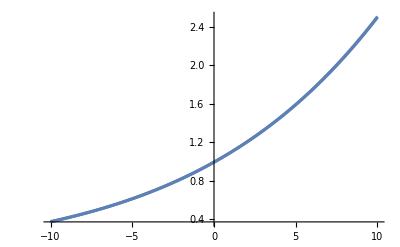

```mathematica
Plot[{R2X/.α->-3/.β->.1/.γ->0/.η->0, R1X+.005/.α->-3/.β->.1/.γ->0/.η->0, rXY1/.α->-3/.β->.1}-.005,{X,-10,10}]
```

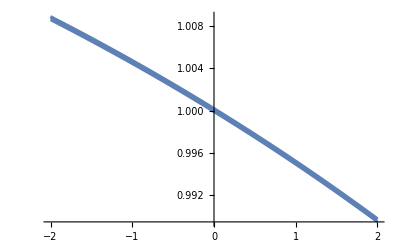

```mathematica
Plot[{R3X/.α->-3/.β->.1/.γ->0/.η->0, R4X+.0001/.α->-3/.β->.1/.γ->0/.η->0, rXY0/.α->-3/.β->.1}-.0001,{X,-2,2}]
```

```mathematica
Plot[{R2X/.α->-2/.β->.1/.γ->0/.η->0, R1X+.005/.α->-2/.β->.1/.γ->0/.η->0, fXY1/.α->-2/.β->.1}-.005,{X,-10,10}]
```

-Graphics-

```mathematica
Plot[{R3X/.α->-2/.β->.3/.γ->0/.η->0, R4X+.0001/.α->-2/.β->.3/.γ->0/.η->0, fXY0/.α->-2/.β->.3}-.0001,{X,-2,2}]
```

-Graphics-

```mathematica
Log[fXY1]
```

Log[fXY1]

```mathematica
Log[fXY0]
```

Log[fXY0]

```mathematica
Dr1xGamma
```

-((0.5 ⅇ^(α+γ) (-2.-12. ⅇ^(2 (α+γ))-2. ⅇ^(4 (α+γ))-4. β^2-8. β η-4. η^2+ⅇ^(α+γ) (-8.-6. β^2-12. β η-6. η^2)+ⅇ^(2 α+2 γ+X (β+η)) (12.-6. β^2-12. β η-6. η^2)+ⅇ^(α+γ+X (β+η)) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(3 α+3 γ+X (β+η)) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(X (β+η)) (2.+1. β^2+2. β η+1. η^2)+ⅇ^(4 α+4 γ+X (β+η)) (2.+1. β^2+2. β η+1. η^2)+ⅇ^(3 (α+γ)) (-8.+2. β^2+4. β η+2. η^2)))/((1.+ⅇ^(α+γ))^3 (1.+ⅇ^(α+γ+X (β+η))) (1.+ⅇ^(2 (α+γ))+0.5 β^2+1. β η+0.5 η^2+ⅇ^(α+γ) (2.-0.5 β^2-1. β η-0.5 η^2))))

```mathematica
fix=(Dr1xGamma + Dr2xGamma)^2/.ω->.001/.α->-3/.β->.1/.γ->1/.η->0
```

(0.00127824 (-3.37104+2.01 ⅇ^(-8+0.1 X)+7.98 ⅇ^(-6+0.1 X)+11.94 ⅇ^(-4+0.1 X)+7.98 ⅇ^(-2+0.1 X)+2.01 ⅇ^(0.1 X))^2)/((1.+ⅇ^(-2+0.1 X))^2)

```mathematica
fix/.X->0 + D[D[fix,X],X]/2/.X->0
```

1.73981×10^-6

```mathematica
xfisher=(Dr1xGamma + Dr2xGamma)^2
```

(0.25 ⅇ^(2 α+2 γ) (-2.-12. ⅇ^(2 (α+γ))-2. ⅇ^(4 (α+γ))-4. β^2-8. β η-4. η^2+ⅇ^(α+γ) (-8.-6. β^2-12. β η-6. η^2)+ⅇ^(2 α+2 γ+X (β+η)) (12.-6. β^2-12. β η-6. η^2)+ⅇ^(α+γ+X (β+η)) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(3 α+3 γ+X (β+η)) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(X (β+η)) (2.+1. β^2+2. β η+1. η^2)+ⅇ^(4 α+4 γ+X (β+η)) (2.+1. β^2+2. β η+1. η^2)+ⅇ^(3 (α+γ)) (-8.+2. β^2+4. β η+2. η^2))^2)/((1.+ⅇ^(α+γ))^6 (1.+ⅇ^(α+γ+X (β+η)))^2 (1.+ⅇ^(2 (α+γ))+0.5 β^2+1. β η+0.5 η^2+ⅇ^(α+γ) (2.-0.5 β^2-1. β η-0.5 η^2))^2)

```mathematica
xfisher /.X->0 + D[D[xfisher,X],X]/2/.X->0/.ω->.001/.α->-3/.β->.1/.γ->1/.η->0
```

1.73981×10^-6

```mathematica
Save["LogisticX_Derivatives.m",{Dr1xGamma,Dr2xGamma,Dr3xGamma,Dr1xEta,Dr3xEta}]
```

```mathematica
Dr2xGamma
```

0

```mathematica
Dr1xGamma
```

-((0.5 ⅇ^(α+γ) (-2.-12. ⅇ^(2 (α+γ))-2. ⅇ^(4 (α+γ))-4. β^2-8. β η-4. η^2+ⅇ^(α+γ) (-8.-6. β^2-12. β η-6. η^2)+ⅇ^(2 α+2 γ+X (β+η)) (12.-6. β^2-12. β η-6. η^2)+ⅇ^(α+γ+X (β+η)) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(3 α+3 γ+X (β+η)) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(X (β+η)) (2.+1. β^2+2. β η+1. η^2)+ⅇ^(4 α+4 γ+X (β+η)) (2.+1. β^2+2. β η+1. η^2)+ⅇ^(3 (α+γ)) (-8.+2. β^2+4. β η+2. η^2)))/((1.+ⅇ^(α+γ))^3 (1.+ⅇ^(α+γ+X (β+η))) (1.+ⅇ^(2 (α+γ))+0.5 β^2+1. β η+0.5 η^2+ⅇ^(α+γ) (2.-0.5 β^2-1. β η-0.5 η^2))))

```mathematica
Dr3xGamma
```

(ⅇ^(α+γ) (2.-2. ⅇ^(X (β+η))-12. ⅇ^(2 α+2 γ+X (β+η))+1. β^2+2. β η+1. η^2+ⅇ^(3 α+3 γ+X (β+η)) (-8.-6. β^2-12. β η-6. η^2)+ⅇ^(2 (α+γ)) (12.-6. β^2-12. β η-6. η^2)+ⅇ^(4 α+4 γ+X (β+η)) (-2.-4. β^2-8. β η-4. η^2)+ⅇ^(α+γ) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(3 (α+γ)) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(4 (α+γ)) (2.+1. β^2+2. β η+1. η^2)+ⅇ^(α+γ+X (β+η)) (-8.+2. β^2+4. β η+2. η^2)))/((1.+ⅇ^(α+γ))^3 (1.+ⅇ^(α+γ+X (β+η))) (2.+ⅇ^(α+γ) (4.-1. β^2-2. β η-1. η^2)+ⅇ^(2 (α+γ)) (2.+1. β^2+2. β η+1. η^2)))

```mathematica
Dr3xEta
```

-(1. ⅇ^(α+γ) (2. ⅇ^(X (β+η)) X-2. β-2. η+ⅇ^(α+γ) (2. β+2. η)+ⅇ^(α+γ+X (β+η)) (-2. β-2. η+X (4.-1. β^2-2. β η-1. η^2))+ⅇ^(2 α+2 γ+X (β+η)) (2. β+2. η+X (2.+1. β^2+2. β η+1. η^2))))/((1.+ⅇ^(α+γ+X (β+η))) (2.+ⅇ^(α+γ) (4.-1. β^2-2. β η-1. η^2)+ⅇ^(2 (α+γ)) (2.+1. β^2+2. β η+1. η^2)))

```mathematica
Dr4xGamma
```

Dr4xGamma

```mathematica
Dr4xGamma=0
```

0

```mathematica
D[Log[R2X],γ]
```

0

```mathematica
R2X
```

1/((1+ⅇ^(-α-X β)) (1/(1+ⅇ^-α)+0.5 ((2 ⅇ^(-2 α) β^2)/((1+ⅇ^-α)^3)-(ⅇ^-α β^2)/((1+ⅇ^-α)^2))))

```mathematica
D[Log[R2X],η]
```

0

```mathematica
Dr2xEta=0
```

0

```mathematica
Dr2xGamma
```

0

```mathematica
Dr4xGamma
```

0

```mathematica
Dr4xEta=0
```

0

```mathematica
Save["~/R21_Collider/Sims/LogisticX_Derivatives.m",{Dr1xGamma,Dr2xGamma,Dr3xGamma,Dr4xGamma,Dr1xEta,Dr2xEta,Dr3xEta,Dr4xEta}];
```

Save::noopen: Cannot open ~/R21_Collider/Sims/LogisticX_Derivatives.m.

```mathematica
Dr1xGamma
```

-((0.5 ⅇ^(α+γ) (-2.-12. ⅇ^(2 (α+γ))-2. ⅇ^(4 (α+γ))-4. β^2-8. β η-4. η^2+ⅇ^(α+γ) (-8.-6. β^2-12. β η-6. η^2)+ⅇ^(2 α+2 γ+X (β+η)) (12.-6. β^2-12. β η-6. η^2)+ⅇ^(α+γ+X (β+η)) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(3 α+3 γ+X (β+η)) (8.-2. β^2-4. β η-2. η^2)+ⅇ^(X (β+η)) (2.+1. β^2+2. β η+1. η^2)+ⅇ^(4 α+4 γ+X (β+η)) (2.+1. β^2+2. β η+1. η^2)+ⅇ^(3 (α+γ)) (-8.+2. β^2+4. β η+2. η^2)))/((1.+ⅇ^(α+γ))^3 (1.+ⅇ^(α+γ+X (β+η))) (1.+ⅇ^(2 (α+γ))+0.5 β^2+1. β η+0.5 η^2+ⅇ^(α+γ) (2.-0.5 β^2-1. β η-0.5 η^2))))

```mathematica
Dr2xGamma
```

0

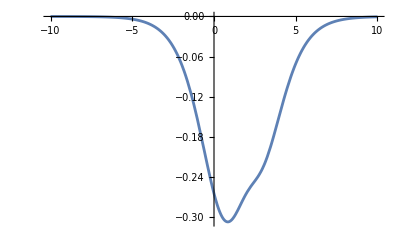

```mathematica
Plot[Dr1xGamma/.X->2/.α->-2.2/.β->.5/.η->.5,{γ,-10,10}]
```

```mathematica
fY1XG0
```

1/(1+ⅇ^(-α-X β))

```mathematica
EXG1Y1
```

EXG1Y1

```mathematica
RY1XG1
```

RY1XG1

```mathematica
myfun=E(X^2 *R1X)- E(X *R1X)^2
```

-(ⅇ X^2)/((1+ⅇ^(-α-X β-γ-X η))^2 (1/(1+ⅇ^(-α-γ))+0.5 ((2 ⅇ^(-2 α-2 γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^3)-(ⅇ^(-α-γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^2)))^2)+(ⅇ X^2)/((1+ⅇ^(-α-X β-γ-X η)) (1/(1+ⅇ^(-α-γ))+0.5 ((2 ⅇ^(-2 α-2 γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^3)-(ⅇ^(-α-γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^2))))

```mathematica
.5*D[D[myfun,X],X]/.X->0/.β->.5/.α->-2.2/.ω->.001
```

0.5 (-(2 ⅇ)/((1+ⅇ^(2.2-γ))^2 (1/(1+ⅇ^(2.2-γ))+0.5 ((2 ⅇ^(4.4-2 γ) (-0.5-η)^2)/((1+ⅇ^(2.2-γ))^3)-(ⅇ^(2.2-γ) (-0.5-η)^2)/((1+ⅇ^(2.2-γ))^2)))^2)+(2 ⅇ)/((1+ⅇ^(2.2-γ)) (1/(1+ⅇ^(2.2-γ))+0.5 ((2 ⅇ^(4.4-2 γ) (-0.5-η)^2)/((1+ⅇ^(2.2-γ))^3)-(ⅇ^(2.2-γ) (-0.5-η)^2)/((1+ⅇ^(2.2-γ))^2)))))

```mathematica
myfun0=X *R2X
```

X/((1+ⅇ^(-α-X β)) (1/(1+ⅇ^-α)+0.5 ((2 ⅇ^(-2 α) β^2)/((1+ⅇ^-α)^3)-(ⅇ^-α β^2)/((1+ⅇ^-α)^2))))

```mathematica
.5*D[D[myfun0,X],X]/.X->0/.β->.5/.α->-2.2/.ω->.001
```

0.412928

```mathematica
.5*D[D[myfun,X],X]/.X->0/.α->-2.2/.ω->.001
```

0.5 (-(2 ⅇ)/((1+ⅇ^(2.2-γ))^2 (1/(1+ⅇ^(2.2-γ))+0.5 ((2 ⅇ^(4.4-2 γ) (-β-η)^2)/((1+ⅇ^(2.2-γ))^3)-(ⅇ^(2.2-γ) (-β-η)^2)/((1+ⅇ^(2.2-γ))^2)))^2)+(2 ⅇ)/((1+ⅇ^(2.2-γ)) (1/(1+ⅇ^(2.2-γ))+0.5 ((2 ⅇ^(4.4-2 γ) (-β-η)^2)/((1+ⅇ^(2.2-γ))^3)-(ⅇ^(2.2-γ) (-β-η)^2)/((1+ⅇ^(2.2-γ))^2)))))

```mathematica
mean1=.5*D[D[myfun,X],X]/.X->0/.α->-2.2/.ω->.001/.γ->1/.η->0
```

0.5 (-0.291295/((0.231475+0.0477691 β^2)^2)+1.25843/(0.231475+0.0477691 β^2))

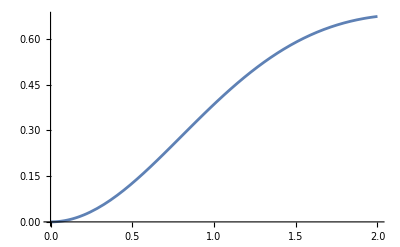

```mathematica
Plot[mean1,{β,0,2}]
```

```mathematica
mean0=.5*D[D[myfun0,X],X]/.X->0/.α->-2.2/.ω->.001
```

(0.0898003 β)/(0.0997505+0.0359425 β^2)

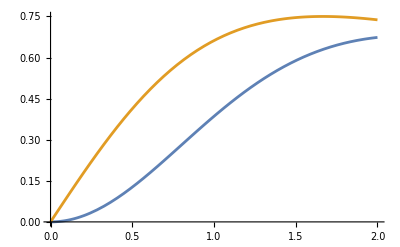

```mathematica
Plot[{mean1,mean0},{β,0,2}]
```

```mathematica
mean1
```

0.5 (-0.291295/((0.231475+0.0477691 β^2)^2)+1.25843/(0.231475+0.0477691 β^2))

```mathematica
mean0
```

(0.0898003 β)/(0.0997505+0.0359425 β^2)

```mathematica
sd1=Sqrt[.5*D[D[X^2*R1X,X],X]- (.5*D[D[X*R1X,X],X])^2]/.X->0/.α->-2.2/.ω->.001/.γ->1/.η->0
```

√(-(0.0316464 β^2)/((0.231475+0.0477691 β^2)^2)+0.231475/(0.231475+0.0477691 β^2))

```mathematica
sd0=Sqrt[.5*D[D[X^2*R2X,X],X]- (.5*D[D[X*R2X,X],X])^2]/.X->0/.α->-2.2/.ω->.001/.γ->1/.η->0
```

√(-(0.0080641 β^2)/((0.0997505+0.0359425 β^2)^2)+0.0997505/(0.0997505+0.0359425 β^2))

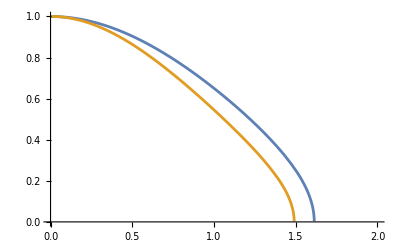

```mathematica
Plot[{sd1,sd0},{β,0,2}]
```

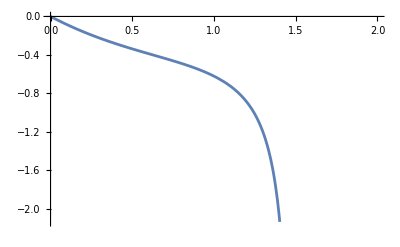

```mathematica
Plot[{Sqrt[1]*mean1/sd1-Sqrt[1]*mean0/sd0},{β,0,2}]
```

```mathematica
myfun1=X*R1X
```

X/((1+ⅇ^(-α-X β-γ-X η)) (1/(1+ⅇ^(-α-γ))+0.5 ((2 ⅇ^(-2 α-2 γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^3)-(ⅇ^(-α-γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^2))))

```mathematica
myfun2=X*R2X
```

X/((1+ⅇ^(-α-X β)) (1/(1+ⅇ^-α)+0.5 ((2 ⅇ^(-2 α) β^2)/((1+ⅇ^-α)^3)-(ⅇ^-α β^2)/((1+ⅇ^-α)^2))))

```mathematica
myfun3=X*R3X
```

((1-1/(1+ⅇ^(-α-X β-γ-X η))) X)/(1-1/(1+ⅇ^(-α-γ))+0.5 (-(2 ⅇ^(-2 α-2 γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^3)+(ⅇ^(-α-γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^2)))

```mathematica
myfun4=X*R4X
```

((1-1/(1+ⅇ^(-α-X β))) X)/(1-1/(1+ⅇ^(-α-γ))+0.5 (-(2 ⅇ^(-2 α) β^2)/((1+ⅇ^-α)^3)+(ⅇ^-α β^2)/((1+ⅇ^-α)^2)))

```mathematica
mean1=(D[D[myfun1,X],X])/.α->-2.2/.ω->.001/.η->0/.γ->1/.X->0
```

0.+(0.355789 β)/(0.231475+0.0477691 β^2)

```mathematica
myfun1
```

X/((1+ⅇ^(-α-X β-γ-X η)) (1/(1+ⅇ^(-α-γ))+0.5 ((2 ⅇ^(-2 α-2 γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^3)-(ⅇ^(-α-γ) (-β-η)^2)/((1+ⅇ^(-α-γ))^2))))

```mathematica
mean2=(D[D[myfun2,X],X])/.α->-2.2/.ω->.001/.η->0/.γ->1/.X->0
```

0.+(0.179601 β)/(0.0997505+0.0359425 β^2)

```mathematica
mean3=(D[D[myfun3,X],X])/.α->-2.2/.ω->.001/.η->0/.γ->1/.X->0
```

0.-(0.355789 β)/(0.768525-0.0477691 β^2)

```mathematica
mean4=(D[D[myfun4,X],X])/.α->-2.2/.ω->.001/.η->0/.γ->1/.X->0
```

0.-(0.179601 β)/(0.768525-0.0359425 β^2)

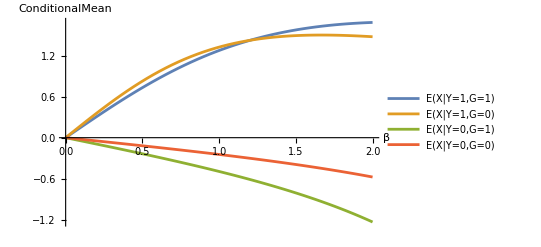

```mathematica
Plot[{mean1,mean2,mean3,mean4},{β,0,2},PlotLegends->{"E(X|Y=1,G=1)","E(X|Y=1,G=0)","E(X|Y=0,G=1)","E(X|Y=0,G=0)"},AxesLabel->{"β","ConditionalMean"}]
```

```mathematica
Show[%393,Axes->True]
```

Show::gtype: Out is not a type of graphics.

Show[%393,Axes→True]

```mathematica
Simplify[mean1-mean2]
```

0.+(-3.54292 β+2.45122 β^3)/(13.4482+7.62099 β^2+1. β^4)

```mathematica
Null Log Likelihood (all obs):  s*(N1*log(omega) +(N2)*log(1-w))  + (1-s) * sum_(N1+N2) l(x_i |Y)
```

```mathematica
Alt Log Likelihood (all obs) :   s*(sum_G1 r(1|x,y=1)) + s*sum_G2 r(0|x,y=1)   + (1-s) *(sum_G1 l(x|g=1,y=1) + sum_G2 l(x|g=0,y=1) )
```

```mathematica
l(g|x,y) = sum_G1 (r(g|x,y)) + n1*l(g)
```

```mathematica
mypdf1=(R1X*PDF[NormalDistribution[0,1]])/.α->-2.2/.ω->.001/.η->0/.γ->1/.β->0.5
```

(4.10817 Function[x,(ⅇ^(-x^2/2))/(√(2 π))])/(1+ⅇ^(1.2-0.5 X))

```mathematica
a=Integrate[mypdf1,{x,-Infinity,t}]
```

Integrate::idiv: Integral of (4.10817 Function[x,(ⅇ^(-x^2/2))/(√(2 π))])/(1+ⅇ^(1.2-0.5 X)) does not converge on {-∞,t}.

Integrate::idiv: Integral of 1 does not converge on {-∞,t}.

(4.10817 Function[x,(ⅇ^(-x^2/2))/(√(2 π))] ∫_(-∞)^t 1ⅆx)/(1+ⅇ^(1.2-0.5 X))

```mathematica
Solve[a-.75==0,t]
```

{{t→(0.243417 (1.+ⅇ^(1.2-0.5 X)) (0.75+(-∞ Function[x,(ⅇ^(-x^2/2))/(√(2 π))])/(1.+ⅇ^(1.2-0.5 X))))/Function[x,(ⅇ^(-x^2/2))/(√(2 π))]}}

```mathematica
cndmeanX1 = (D[D[myfun1,X],X]);
```

```mathematica
cndmeanX2 = (D[D[myfun2,X],X]);
```

```mathematica
cndmeanX3 = (D[D[myfun3,X],X]);
```

```mathematica
cndmeanX4 = (D[D[myfun4,X],X]);
```

```mathematica
CForm[cndmeanX1]
```

(-2*Power(E,-α - X*β - γ - X*η)*(-β - η))/
    (Power(1 + Power(E,-α - X*β - γ - X*η),2)*(1/(1 + Power(E,-α - γ)) + 
        0.5*((2*Power(E,-2*α - 2*γ)*Power(-β - η,2))/Power(1 + Power(E,-α - γ),3) - (Power(E,-α - γ)*Power(-β - η,2))/Power(1 + Power(E,-α - γ),2)))) + 
   (2*Power(E,-2*α - 2*X*β - 2*γ - 2*X*η)*X*Power(-β - η,2))/
    (Power(1 + Power(E,-α - X*β - γ - X*η),3)*(1/(1 + Power(E,-α - γ)) + 
        0.5*((2*Power(E,-2*α - 2*γ)*Power(-β - η,2))/Power(1 + Power(E,-α - γ),3) - (Power(E,-α - γ)*Power(-β - η,2))/Power(1 + Power(E,-α - γ),2)))) - 
   (Power(E,-α - X*β - γ - X*η)*X*Power(-β - η,2))/
    (Power(1 + Power(E,-α - X*β - γ - X*η),2)*(1/(1 + Power(E,-α - γ)) + 
        0.5*((2*Power(E,-2*α - 2*γ)*Power(-β - η,2))/Power(1 + Power(E,-α - γ),3) - (Power(E,-α - γ)*Power(-β - η,2))/Power(1 + Power(E,-α - γ),2))))

```mathematica
CForm[cndmeanX2]
```

(2*Power(E,-α - X*β)*β)/(Power(1 + Power(E,-α - X*β),2)*(1/(1 + Power(E,-α)) + 
        0.5*((2*Power(β,2))/(Power(E,2*α)*Power(1 + Power(E,-α),3)) - Power(β,2)/(Power(E,α)*Power(1 + Power(E,-α),2))))) + 
   (2*Power(E,-2*α - 2*X*β)*X*Power(β,2))/
    (Power(1 + Power(E,-α - X*β),3)*(1/(1 + Power(E,-α)) + 0.5*
         ((2*Power(β,2))/(Power(E,2*α)*Power(1 + Power(E,-α),3)) - Power(β,2)/(Power(E,α)*Power(1 + Power(E,-α),2))))) - 
   (Power(E,-α - X*β)*X*Power(β,2))/
    (Power(1 + Power(E,-α - X*β),2)*(1/(1 + Power(E,-α)) + 0.5*
         ((2*Power(β,2))/(Power(E,2*α)*Power(1 + Power(E,-α),3)) - Power(β,2)/(Power(E,α)*Power(1 + Power(E,-α),2)))))

```mathematica
CForm[cndmeanX3]
```

(2*Power(E,-α - X*β - γ - X*η)*(-β - η))/
    (Power(1 + Power(E,-α - X*β - γ - X*η),2)*(1 - 1/(1 + Power(E,-α - γ)) + 
        0.5*((-2*Power(E,-2*α - 2*γ)*Power(-β - η,2))/Power(1 + Power(E,-α - γ),3) + (Power(E,-α - γ)*Power(-β - η,2))/Power(1 + Power(E,-α - γ),2)))) - 
   (2*Power(E,-2*α - 2*X*β - 2*γ - 2*X*η)*X*Power(-β - η,2))/
    (Power(1 + Power(E,-α - X*β - γ - X*η),3)*(1 - 1/(1 + Power(E,-α - γ)) + 
        0.5*((-2*Power(E,-2*α - 2*γ)*Power(-β - η,2))/Power(1 + Power(E,-α - γ),3) + (Power(E,-α - γ)*Power(-β - η,2))/Power(1 + Power(E,-α - γ),2)))) + 
   (Power(E,-α - X*β - γ - X*η)*X*Power(-β - η,2))/
    (Power(1 + Power(E,-α - X*β - γ - X*η),2)*(1 - 1/(1 + Power(E,-α - γ)) + 
        0.5*((-2*Power(E,-2*α - 2*γ)*Power(-β - η,2))/Power(1 + Power(E,-α - γ),3) + (Power(E,-α - γ)*Power(-β - η,2))/Power(1 + Power(E,-α - γ),2))))

```mathematica
CForm[cndmeanX4]
```

(-2*Power(E,-α - X*β)*β)/(Power(1 + Power(E,-α - X*β),2)*(1 - 1/(1 + Power(E,-α - γ)) + 
        0.5*((-2*Power(β,2))/(Power(E,2*α)*Power(1 + Power(E,-α),3)) + Power(β,2)/(Power(E,α)*Power(1 + Power(E,-α),2))))) - 
   (2*Power(E,-2*α - 2*X*β)*X*Power(β,2))/
    (Power(1 + Power(E,-α - X*β),3)*(1 - 1/(1 + Power(E,-α - γ)) + 
        0.5*((-2*Power(β,2))/(Power(E,2*α)*Power(1 + Power(E,-α),3)) + Power(β,2)/(Power(E,α)*Power(1 + Power(E,-α),2))))) + 
   (Power(E,-α - X*β)*X*Power(β,2))/
    (Power(1 + Power(E,-α - X*β),2)*(1 - 1/(1 + Power(E,-α - γ)) + 
        0.5*((-2*Power(β,2))/(Power(E,2*α)*Power(1 + Power(E,-α),3)) + Power(β,2)/(Power(E,α)*Power(1 + Power(E,-α),2)))))